```mathematica
SetDirectory["/home/xidad/CLionProjects/ArrayVsVector"]
```

/home/xidad/CLionProjects/ArrayVsVector

```mathematica
arr = Import["arr","Table"];
vect = Import["vector","Table"];
```

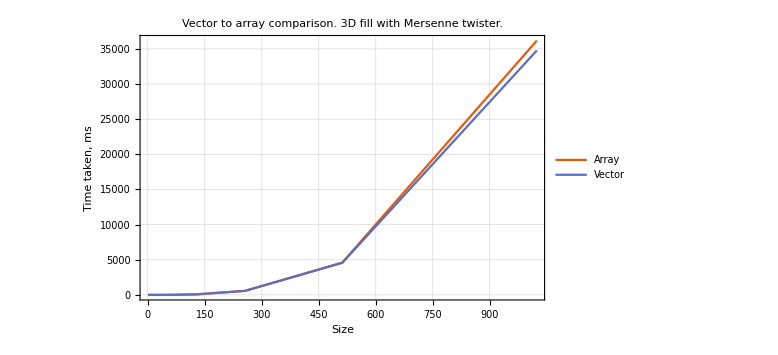

```mathematica
plt = ListLinePlot[{arr,vect},PlotTheme->"Scientific",PlotLegends->{"Array","Vector"},ImageSize->Large,GridLines->Automatic,PlotRange->Full,Joined->True,PlotLabel->"Vector to array comparison. 3D fill with Mersenne twister.", FrameLabel->{"Size","Time taken, ms"}]
```